```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=0.01;u0=10^-10;a=0.01;δstart=10^-10;αSch=200;m=100;
V=-α/r;Vs=-0.01/r Erf[r/(√2 a)]-2π 0.01c a^2(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3)/.{a->0.01,c->1.009403159725795938};
```

```mathematica
EigenEnergy[V_,αSch_]:=
Module[{min=1.*10^-19,max=2000,wpc=50,acg=30,sol,ef,evShifted,evnew,steps=∞,stepfraction=10^-2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
(*Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*)},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=Riffle[(ev-shift),evShifted]];
Print[evShifted];*)
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,(*MaxStepFraction->stepfraction,*)WorkingPrecision->wpc,AccuracyGoal->acg];
evnew=e/.#&/@
ParallelTable[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.95 SetPrecision[evShifted[[n]],3],1.05 SetPrecision[evShifted[[n]],3]},WorkingPrecision->wpc,AccuracyGoal->acg,StepMonitor:>PrintTemporary[e]],{n,20}]
]
```

```mathematica
EigenEnergy[V,αSch]
```

Eigensystem::chnpdef: 警告：可能第一个参数中的第二个矩阵 SparseArray[Automatic,«2»,{1,{{«1»},{«1»}},{0.0266667,-0.00333333,0.00666667,0.00666667,-0.00333333,0.0266667,«79980»,0.00666667,0.00666667,0.0533333,0.00666667,0.0533333}}] 不是正定的，这对于用 Arnoldi 方法给出准确结果是必要的.

{-0.00499999,-0.00125,-0.000555555,-0.0003125,-0.0002,-0.000138889,-0.000102041,-0.000078125,-0.0000617284,-0.00005,-0.0000413223,-0.0000347222,-0.0000295858,-0.0000255102,-0.0000222222,-0.0000195313,-0.000017301,-0.0000154321,-0.0000138503,-0.0000124995}

1

4

7

10

ParametricNDSolve::precw: The precision of the differential equation ({{-(0.01 u[r$1629])/r$1629-u''[r$1629]/200==e$1628 u[r$1629],u'[2000]==-1.×10^-19,u[2000]==1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (50.).

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000063476503974144581821703510978258607872595469202956; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000029023992328318183758201870968020459564001346301329; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000036675704160085130143992131331727854250626748401622; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.00020445669534040503965072469156534723995148230630454; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0000475

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.00021573550089234240944055442416938347181135998616548; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0000969388

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000063436954487477551844841999355599540686651894942342; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.0000475001

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.00033383202967138094536023568841850549738588774581602; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.000296875

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000028952909482483148409423969710028111865601584670771; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.0000969388

-0.00005

-0.000102041

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000036675704164159082562154084650792555849416289098142; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.000296875

-0.00005

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000018298972451426279072768445826776605719397974559339; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.000102041

-0.000296875

-0.000102041

-0.000296875

-0.00004999999979237278592385240738594

-0.0003125

-0.00004999999999999220426801695114034

-0.0001020408163265419865988262171363

-0.00005000000000000000207966840771953

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000039928146021272817267138775092425870745371032342138; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00474999

-0.0003125

-0.0001020408163265306164484535218188

-0.00005000000000000000207966821197581

-0.0001020408163265306164873695636391

-0.0001020408163265306164873695641899

-0.0001020408163265306164873695641899

-0.00005000000000000000207966819521947882956081200582709

-0.0000500000000000000020796682119758110910003905878137

-0.0003125000811129782112875175048572

-0.00005000000000000000207966820680225577665570434505487

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000018298972451426279072768445826776605719397974559339; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00005000000000000000207966820680225577665570434505487

-0.0003124999999943542280696441445938

8

-0.000050000000000000002079668204703555294161720314265855

-0.0003124999999999996347266361261122

-0.000050000000000000002079668204703555294161720314265855

-0.0000742187

-0.000050000000000000002079668204703555294161720314265855

-0.0003125000000000000129791762075116

-0.0000742187

-0.000050000000000000002079668204906153388501231900074642

-0.0003125000000000000129791762700884

-0.000078125

-0.000050000000000000002079668204906153388501231900074642

-0.000078125

-0.000050000000000000002079668204958618679273887050366637

-0.0003125000000000000129791762700884

-0.000050000000000000002079668204958618679273887050366637

-0.000078125

-0.000050000000000000002079668204958618679273887050366637

-0.000050000000000000002079668204958618679273887050366637

-0.000050000000000000002079668204961720519607854239798431

-0.00007812500000000062504255243789331

-0.004749991483715376196228508121067

-0.000050000000000000002079668204963432522764088038055643

-0.00031250000000000001297917627008845031172758632410283

-0.000050000000000000002079668204964288524342204937184249

-0.00031250000000000001297917627008845031249074317966615

-0.000050000000000000002079668204964716525131263386748552

-0.000078125000000000003248171971774564768778131108527003

-0.000050000000000000002079668204964716525131263386748552

-0.000078125000000000003248700320431329752611622660249175

5

-0.000050000000000000002079668204964818202153840568521997

-0.000078125000000000003248700320419347316095957370093186

9

-0.00005000000000000000207966820496487436383981659002635

-0.004999991035489870228047948330641

-0.00019

-0.00005000000000000000207966820496487436383981659002635

-0.00005000000000000000207966820496487436383981659002635

-0.000058642

-0.00019

-0.000050000000000000002079668204964880702827777231905619

-0.000058642

-0.0002

-0.000050000000000000002079668204964880702827777231905619

-0.0000617284

-0.000050000000000000002079668204964882366426686693722356

-0.0002

-0.0000617284

-0.000050000000000000002079668204964883285330725601270449

-0.004999991035489870228047948330641

-0.0002

-0.0000617284

-0.000050000000000000002079668204964883744782745055044496

-0.0000617284

-0.000050000000000000002079668204964883744782745055044496

-0.0000617284

-0.000050000000000000002079668204964883853930656954951712

-0.000050000000000000002079668204964883914219705868441615

-0.0002000000000036368302466782687077

-0.000050000000000000002079668204964883944364230325186567

-0.00006172839506172839762860606126821

-0.0001999999999999997865665685089183

-0.000050000000000000002079668204964883959436492553559043

-0.004999991035489870363262058007547

-0.00006172839506172839762894566330077

-0.0002000000000000000083106716572314

-0.000050000000000000002079668204964883966972623667745281

-0.00006172839506172839762894566330077

-0.0000500000000000000020796682049648839707406892248384

-0.0002000000000000000083106726764408

-0.00006172839506172839762894567653544

-0.000050000000000000002079668204964883972624722003384959

-0.0002000000000000000083106726764408

-0.00006172839506172839762894567653746

-0.000050000000000000002079668204964883973566738392658239

-0.00006172839506172839762894567653746

-0.000050000000000000002079668204964883974037746587294879

-0.00500000001614871709617483663166

-0.000050000000000000002079668204964883974273250684613199

-0.000050000000000000002079668204964883974273250684613199

-0.000061728395061728397628945676537457612623079327384167

-0.000050000000000000002079668204964883974273250684613199

6

13

-0.000050000000000000002079668204964883974273250684613199

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000078233083552440909133598515024008309638833894813533; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.000050000000000000002079668204964883974273250684613199

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.00016350534363365434842621826241264855789110383583624; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0000281065

-0.000131944

-0.000050000000000000002079668204964883974279251213005361

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000082817289851978444613810539390817074115904243981781; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.0000281069

-0.004999999999970936066825758175975

-0.000050000000000000002079668204964883974279251213005361

-0.000131944

-0.000029586

-0.000029586

-0.000050000000000000002079668204964883974280825985297292

-0.000138889

-0.000050000000000000002079668204964883974281695828108814

-0.0000295858

-0.000138889

-0.000050000000000000002079668204964883974282130749514575

-0.0000295858

-0.0000295858

-0.000050000000000000002079668204964883974282348210217456

-0.000138889

-0.00500000000000000011202172394524

-0.000050000000000000002079668204964883974282348210217456

-0.0000295858

-0.00005000000000000000207966820496488397428239987041322

-0.000050000000000000002079668204964883974282428405491058

-0.00002958579881656804856770999604703

-0.0001388888888891230764376788497927

-0.000050000000000000002079668204964883974282428405491058

-0.00002958579881656804856812409714184

-0.0001388888888888888911977142669993

-0.000050000000000000002079668204964883974282428405491058

-0.00002958579881656804856812409714184

-0.000050000000000000002079668204964883974282428405491058

-0.000050000000000000002079668204964883974282428405491058

-0.000029585798816568048568124097141838121929794682245173

-0.000050000000000000002079668204964883974282428405491058

-0.000029585798816568048568124098401999558093362683391941

-0.00013888888888888889466204122571484447463219804476242

-0.000029585798816568048568124100318746741751252672747587

-0.000050000000000000002079668204964883974282428750933221

-0.0001388888888888888946620411533536792507837234169643

-0.000029585798816568048568124100665063046433275731951577

-0.000050000000000000002079668204964883974282428941742003

-0.000029585798816568048568124100838221198774287261553573

-0.000138888888888888894662041153353664140866058989019

-0.000029585798816568048568124100838221198774287261553573

-0.000050000000000000002079668204964883974282428941742003

-0.000029585798816568048568124100840827735135479209963222

-0.00013888888888888889466204115335366414018665367060453

-0.000050000000000000002079668204964883974282428941742003

-0.000029585798816568048568124100882814005040136118158896

-0.00013888888888888889466204115335366414018665367060453

-0.000050000000000000002079668204964883974282428941742003

-0.000029585798816568048568124100903807139992464572256733

15

-0.000029585798816568048568124100914303707468628799305652

-0.000050000000000000002079668204964883974282428951974559

-0.000029585798816568048568124100919551991206710912830111

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000095109021678020119790464392785026574181174961027911; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.000050000000000000002079668204964883974282428951974559

-0.000029585798816568048568124100922176133075751969592341

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.00012972162675559080803422528086981169952061682733585; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0000211111

-0.000050000000000000002079668204964883974282428951974559

-0.000029585798816568048568124100923488204010272497973455

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000077859113174591196025449540131332034560191025573182; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.000021112

-0.000029585798816568048568124100923488204010272497973455

-0.000050000000000000002079668204964883974282428953250462

-0.0000222227

-0.000029585798816568048568124100923502447737721078120635

-0.0050000000000000002061668198994761033159987521764984

-0.000050000000000000002079668204964883974282428953250462

-0.000029585798816568048568124100923823343607626920142324

-0.0000222227

-0.000029585798816568048568124100923983791542579841153168

-0.000050000000000000002079668204964883974282428953585309

-0.0000222222

-0.000029585798816568048568124100924064015510056301658591

-0.000050000000000000002079668204964883974282428953770265

-0.000029585798816568048568124100924104127493794531911302

-0.0000222222

-0.000029585798816568048568124100924104127493794531911302

-0.000050000000000000002079668204964883974282428953770265

-0.000029585798816568048568124100924104583284027619959297

-0.000050000000000000002079668204964883974282428953814204

-0.000029585798816568048568124100924114383384845633498477

-0.000029585798816568048568124100924114383384845633498477

-0.000050000000000000002079668204964883974282428953814204

-0.00002222222222222225378033579057391

-0.0050000000000000002061668198499977123677702851201745

-0.000029585798816568048568124100924114485636246487678433

-0.000050000000000000002079668204964883974282428953814204

-0.00002958579881656804856812410092411688453575056397325

-0.000050000000000000002079668204964883974282428953814204

-0.000029585798816568048568124100924118083985502602120659

-0.000029585798816568048568124100924118683710378621194363

-0.000050000000000000002079668204964883974282428953814204

-0.000022222222222222223146807897724847141970075726520959

-0.000029585798816568048568124100924118983572816630731215

-0.000022222222222222223146815492639562219285193511063991

-0.00005000000000000000207966820496488397428242895381544

-0.000029585798816568048568124100924118983572816630731215

-0.000022222222222222223146815483880822858470259484858877

-0.000029585798816568048568124100924118986701419269281792

-0.00005000000000000000207966820496488397428242895381544

-0.000029585798816568048568124100924119060102727452390716

-0.000022222222222222223146815483880822858470259484858877

-0.000050000000000000002079668204964883974282428953815765

2

-0.000029585798816568048568124100924119060102727452390716

-0.000022222222222222223146815480010165447680482846025772

-0.000029585798816568048568124100924119060868556739359322

-0.000050000000000000002079668204964883974282428953815944

-0.000022222222222222223146815477753185287976002917646681

-0.00002958579881656804856812410092411907883596914165225

-0.000050000000000000002079668204964883974282428953815944

-0.00002958579881656804856812410092411907883596914165225

-0.000022222222222222223146815480010165447680482846025772

-0.000029585798816568048568124100924119079023431322626194

-0.000050000000000000002079668204964883974282428953815987

-0.000022222222222222223146815479651685078054738370604055

-0.000029585798816568048568124100924119079023431322626194

-0.00005000000000000000207966820496488397428242895381601

-0.000022222222222222223146815479651685078054738370604055

-0.000029585798816568048568124100924119079115206534978983

-0.000029585798816568048568124100924119079115206534978983

-0.000022222222222222223146815479651685078054738370604055

-0.000050000000000000002079668204964883974282428953816022

-0.000029585798816568048568124100924119079160136608649715

-0.000022222222222222223146815479613510575776259112254982

-0.000050000000000000002079668204964883974282428953816028

-0.0011875

-0.000029585798816568048568124100924119080214258271247717

-0.000022222222222222223146815479613510575776259112254982

-0.000029585798816568048568124100924119080741319102546718

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

11

-0.000029585798816568048568124100924119080741319102546718

-0.000022222222222222223146815479613510575776259112254982

-0.000029585798816568048568124100924119080746818167738816

-0.000022222222222222223146815479612229250984431543138683

-0.0000392562

-0.000029585798816568048568124100924119080746818167738816

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080749510326088476

-0.0000392563

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080812672084527997

-0.000029585798816568048568124100924119080812672084527997

-0.0000413224

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080813331079859408

-0.0000413224

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080828792021803583

-0.00002958579881656804856812410092411908083652249277567

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080840387728261713

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080842320346004735

-0.001187499127760638286538400304436

-0.00004132231253494746125998204888674

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080843286654876246

-0.000022222222222222223146815479612229250984431543138683

-0.00004132231404938624848523340942201

-0.000029585798816568048568124100924119080843769809312001

-0.000029585798816568048568124100924119080843769809312001

-0.0000413223140495867785785397226721

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080843774850281812

-0.00004132231404958677857838844567283

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080843774850281812

-0.001187499127760639589709813234069

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080843777318171988

-0.000029585798816568048568124100924119080843777318171988

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080843778526368456

-0.000041322314049586778578388445661300993674280057116641

-0.000022222222222222223146815479612229250984431543138683

-0.000029585798816568048568124100924119080843778526368456

12

-0.000022222222222222223146815479612229250984431543138683

-0.001249999081853304202401039751338

-0.000029585798816568048568124100924119080843779117861027

-0.000022222222222222223146815479612229250831101915205728

-0.000029585798816568048568124100924119080843779117861027

-0.000022222222222222223146815479612229250712924417395062

-0.000029585798816568048568124100924119080843779407436002

-0.0000329861

-0.000029585798816568048568124100924119080843779407436002

-0.000022222222222222223146815479612229250712924417395062

-0.0000329863

-0.000029585798816568048568124100924119080843779549202222

-0.001249999081853304202401039751338

-0.000022222222222222223146815479612229250712924417395062

-0.000029585798816568048568124100924119080843782875233826

-0.0000347223

-0.000022222222222222223146815479612229250703776007353537

-0.000029585798816568048568124100924119080843784538249628

-0.0000347223

-0.000022222222222222223146815479612229250703776007353537

-0.000029585798816568048568124100924119080843785369757528

-0.000022222222222222223146815479612229250703776007353537

-0.0000347222

-0.000029585798816568048568124100924119080843785785511479

-0.000022222222222222223146815479612229250702684433183452

-0.001249999081856568911721780792471

-0.000029585798816568048568124100924119080843785993388454

-0.0000347222

-0.000022222222222222223146815479612229250701843110018057

-0.000029585798816568048568124100924119080843785993388454

-0.0000347222

-0.00002222222222222222314681547961222925070142244843536

-0.000029585798816568048568124100924119080843785995557329

-0.000029585798816568048568124100924119080843785995557329

-0.000022222222222222223146815479612229250701212117644012

-0.0000347222

-0.000029585798816568048568124100924119080843785996619138

-0.000022222222222222223146815479612229250701212117644012

-0.001250000000340756127951575288072

-0.000029585798816568048568124100924119080843785996619138

-0.000022222222222222223146815479612229250701170738154164

-0.000029585798816568048568124100924119080843785997138964

-0.000022222222222222223146815479612229250701138845201251

-0.0000295857988165680485681241009241190808437860093348

-0.000022222222222222223146815479612229250701122898724794

-0.000029585798816568048568124100924119080843786015432718

-0.0000347222222222222236664380127295

-0.000022222222222222223146815479612229250701114925486566

-0.001249999999999873608858173655748

-0.000029585798816568048568124100924119080843786018481677

-0.000022222222222222223146815479612229250701110938867452

-0.00003472222222222222366666774126751

-0.000029585798816568048568124100924119080843786020006157

-0.000022222222222222223146815479612229250701110938867452

-0.000029585798816568048568124100924119080843786020768397

-0.00003472222222222222366666774126751

-0.000022222222222222223146815479612229250701110154559999

-0.000029585798816568048568124100924119080843786020768397

-0.001250000000000000051774293095284

-0.000022222222222222223146815479612229250701109550058947

-0.00002958579881656804856812410092411908084378602077635

-0.000022222222222222223146815479612229250701109550058947

-0.000029585798816568048568124100924119080843786020962933

-0.000029585798816568048568124100924119080843786020962933

-0.000022222222222222223146815479612229250701109550058947

-0.000029585798816568048568124100924119080843786020962933

-0.000034722222222222223666667741276064430121706517978051

-0.000022222222222222223146815479612229250701109503264938

-0.000029585798816568048568124100924119080843786020962974

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

14

-0.000022222222222222223146815479612229250701109503264938

-0.000034722222222222223666667741276058293301497111954544

-0.000022222222222222223146815479612229250701109503264938

-0.000034722222222222223666667741276058293353930192750214

-0.0000242347

-0.000022222222222222223146815479612229250701109503264938

-0.0000242353

-0.000034722222222222223666667741276058293336452499151657

-0.00002222222222222222314681547961222925070110950106791

-0.0000255105

-0.000022222222222222223146815479612229250701109499374561

17

-0.0000255105

-0.000022222222222222223146815479612229250701109498527886

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000088535090648575520572577971346560119972726526957949; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.000022222222222222223146815479612229250701109498104549

-0.0000255102

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.00011452922078277450102142511511633157825714591192044; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.000016436

-0.0012500000000000000517917033504520380828167618883876

-0.000022222222222222223146815479612229250701109497892881

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000089409802351578787249008029893093847431464377964367; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.0000164376

-0.0000255102

-0.000022222222222222223146815479612229250701109497787046

-0.0000173018

-0.000022222222222222223146815479612229250701109497734129

-0.0000173018

-0.000022222222222222223146815479612229250701109497734129

-0.0012500000000000000517917033442785659487244770817422

-0.00002551020408163265739526735786935

-0.0000173009

-0.000022222222222222223146815479612229250701109497734129

-0.000017301

-0.000022222222222222223146815479612229250701109497734129

-0.000022222222222222223146815479612229250701109497734129

-0.000025510204081632654122570980760932471637626661959227

3

-0.000022222222222222223146815479612229250701109497733495

-0.000025510204081632654122571231253697348794019158083172

-0.00001730103806228461602425075516187

-0.000022222222222222223146815479612229250701109497733495

-0.00001730103806228373774275260499509

-0.000022222222222222223146815479612229250701109497733303

-0.000025510204081632654122571231253713428015339184000397

-0.000022222222222222223146815479612229250701109497733303

-0.00001730103806228373774411477380156

-0.000025510204081632654122571231253713413927077350230848

-0.000022222222222222223146815479612229250701109497733244

-0.00001730103806228373774411477409464

-0.000025510204081632654122571231253713413900678401961134

-0.000022222222222222223146815479612229250701109497733244

-0.000527778

-0.00002551020408163265412257123125371341391123798126902

-0.000022222222222222223146815479612229250701109497733227

19

-0.000022222222222222223146815479612229250701109497733213

-0.00001730103806228373774411477409464455146928123773636

-0.000527778

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000094738318105884735592040069200561252442840597669774; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.000022222222222222223146815479612229250701109497733206

-0.000017301038062283737744114775937064387844086265760428

-0.000022222222222222223146815479612229250701109497733203

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.00012382847032521930651907558586165145226057945316257; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0000131578

-0.000017301038062283737744114775937064387844086265760428

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

16

ParametricNDSolve::nderr: Error test failure at r$1629 == 0.000092037646701152207618469607414468927619331638169546; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.0000131605

-0.000527778

-0.000017301038062283737744114776195042695492042824291143

-0.0000138517

-0.0000185547

-0.000017301038062283737744114777194751212047975620067044

-0.0000138517

-0.0000185559

-0.000017301038062283737744114777194751212047975620067044

-0.0000138502

-0.000555555

-0.0000195318

-0.000017301038062283737744114777194751212047975620067044

-0.0000138504

-0.0000195318

-0.000017301038062283737744114777194751212047975620067044

-0.0000195312

-0.000555555

-0.000017301038062283737744114777223082839045942310857977

-0.000017301038062283737744114777194751212047975620067044

-0.0000195312

-0.00001385041551247857523690432124397

-0.000017301038062283737744114777194751212047975620067044

-0.000555555

-0.00001385041551246537446023154602422

-0.000017301038062283737744114777195957976613514303233722

-0.00001953125000000010882679306323251

-0.000017301038062283737744114777197911523447264956980342

-0.000017301038062283737744114777197082523023593555374157

-0.000013850415512465374537566633983366386911692944164658

-0.00001730103806228373774411477719652024981855392930394

-0.000019531250000000000812595284780912499972316433002494

-0.000013850415512465374537566624967445850683008648195007

-0.0000195312500000000008126633471523161347638304012985

-0.000017301038062283737744114777196239113216034116268831

-0.000013850415512465374537566629097769830253668745371233

-0.0000195312500000000008126633471523161347638304012985

-0.000017301038062283737744114777196239113216034116268831

-0.000013850415512465374537566631907399438375590433880413

-0.0000195312500000000008126633471523161347638304012985

-0.000017301038062283737744114777196239113216034116268831

-0.000013850415512465374537566629097769830253668745371233

-0.000019531250000000000812663346282253253434702315655565

-0.000017301038062283737744114777196239113216034116268831

-0.0005555555556003807012727113701089

-0.000013850415512465374537566629730666591303906679055219

-0.000019531250000000000812663346282253253434702315655565

-0.000013850415512465374537566629730666591303906679055219

-0.000017301038062283737744114777196239113216034116268831

-0.000019531250000000000812663346106193372775276691509361

-0.000013850415512465374537566629730666591303906679055219

-0.000017301038062283737744114777196239113216034116268831

-0.0005555555555555481538183334585897

-0.000019531250000000000812663346282253253434702315655565

-0.000013850415512465374537566629730666591303906679055219

-0.000017301038062283737744114777196239113216034116268831

-0.000019531250000000000812663346282253253434702315655565

-0.000013850415512465374537566629731793715354638380595417

-0.000017301038062283737744114777196239113216034116268831

-0.000019531250000000000812663346274034977643843156737467

-0.0005555555555555555786109236132491

-0.000013850415512465374537566629730666591303906679055219

-0.000017301038062283737744114777196239113216034116268831

-0.000019531250000000000812663346265590444948400922786481

-0.000013850415512465374537566629730666591303906679055219

-0.000019531250000000000812663346262711458523422889811724

-0.000017301038062283737744114777196239163641852509278661

-0.000013850415512465374537566629730666591303906679055219

-0.0005555555555555555786111274805331

-0.000013850415512465374537566629730666591303906679055219

-0.000019531250000000000812663346262711458523422889811724

-0.000017301038062283737744114777196239163641852509278661

-0.000013850415512465374537566629730666591303906679055219

-0.000019531250000000000812663346262711458523422889811724

-0.000017301038062283737744114777196239182439595353700503

-0.000019531250000000000812663346262711458523422889811724

-0.0005555555555555555786111274805331

-0.000013850415512465374537566629730667165641605121211436

-0.000017301038062283737744114777196239182439595353700503

-0.000019531250000000000812663346262708920679162883758637

-0.000013850415512465374537566629730669074205086851603708

-0.000019531250000000000812663346262708920679162883758637

-0.000017301038062283737744114777196239187841357534937438

-0.0005555555555555555786111274805686

-0.000019531250000000000812663346262709479728431747495881

-0.000013850415512465374537566629730670028486827716799844

-0.000017301038062283737744114777196239191549760485714966

-0.000019531250000000000812663346262709298329575369980828

-0.000013850415512465374537566629730670505627698149397912

-0.000019531250000000000812663346262709041035506398311179

-0.000017301038062283737744114777196239193403961961103731

-0.000013850415512465374537566629730670505627698149397912

-0.00001953125000000000081266334626270909554191691173142

-0.000017301038062283737744114777196239194331062698798113

-0.000013850415512465374537566629730670567050975618999422

-0.000019531250000000000812663346262709132612228897938712

-0.000017301038062283737744114777196239194794613067645304

-0.000019531250000000000812663346262709151147384891042357

-0.000013850415512465374537566629730670655624554492348184

-0.00001953125000000000081266334626270916041496288759418

-0.000013850415512465374537566629730670655624554492348184

-0.0000173010380622837377441147771962391950263882520689

-0.000019531250000000000812663346262709165048751885870092

-0.000013850415512465374537566629730670667124903140062252

-0.000017301038062283737744114777196239195142275844280698

-0.000019531250000000000812663346262709165048751885870092

-0.000013850415512465374537566629730670683518123534542409

-0.000017301038062283737744114777196239195142275844280698

-0.000019531250000000000812663346262709165048751885870092

-0.000013850415512465374537566629730670683518123534542409

-0.000017301038062283737744114777196239195142275844280698

-0.000019531250000000000812663346262709165048751885870092

-0.000013850415512465374537566629730670683518123534542409

-0.000017301038062283737744114777196239195142275844280698

-0.000019531250000000000812663346262709164962758694048102

-0.000013850415512465374537566629730670683518123534542409

-0.000017301038062283737744114777196239195142275844280698

-0.000019531250000000000812663346262709164962758694048102

-0.000013850415512465374537566629730670683518123534542409

-0.000017301038062283737744114777196239195142275844280698

-0.000019531250000000000812663346262709164962758694048102

-0.000013850415512465374537566629730670683554263025439178

-0.000017301038062283737744114777196239195142275844280698

-0.000019531250000000000812663346262709164961831413058278

-0.000017301038062283737744114777196239195142275844280698

-0.000013850415512465374537566629730670683605878516918952

-0.000019531250000000000812663346262709164961831413058278

-0.000017301038062283737744114777196239195142433008432915

-0.000013850415512465374537566629730670683631686262658839

-0.00001953125000000000081266334626270916496142105491381

-0.000017301038062283737744114777196239195142433008432915

-0.000013850415512465374537566629730670683631686262658839

-0.00001953125000000000081266334626270916495936900199039

-0.000013850415512465374537566629730670683631686262658839

-0.000017301038062283737744114777196239195142433008432915

-0.00001953125000000000081266334626270916495936900199039

-0.000013850415512465374537566629730670683632553917683196

-0.000017301038062283737744114777196239195142452189078036

-0.00001953125000000000081266334626270916495936900199039

-0.000013850415512465374537566629730670683632553917683196

-0.000019531250000000000812663346262709164959322834313209

-0.000017301038062283737744114777196239195142465266383746

-0.000013850415512465374537566629730670683632875250849066

-0.00001953125000000000081266334626270916495923701969313

-0.000017301038062283737744114777196239195142471805036601

-0.000013850415512465374537566629730670683632875250849066

-0.000019531250000000000812663346262709164959194112383091

-0.000017301038062283737744114777196239195142471805036601

-0.000019531250000000000812663346262709164959172658728071

-0.000013850415512465374537566629730670683632994255491135

-0.000017301038062283737744114777196239195142471805036601

-0.000019531250000000000812663346262709164959161931900561

-0.000013850415512465374537566629730670683633164219936086

-0.000017301038062283737744114777196239195142471805036601

-0.000019531250000000000812663346262709164959156568486806

-0.000013850415512465374537566629730670683633249202158562

-0.000017301038062283737744114777196239195142471805036601

-0.000019531250000000000812663346262709164959153886779929

-0.000013850415512465374537566629730670683633249202158562

-0.000017301038062283737744114777196239195142471909789697

-0.00001953125000000000081266334626270916495915254592649

-0.000013850415512465374537566629730670683633260220398028

-0.000017301038062283737744114777196239195142471909789697

-0.000019531250000000000812663346262709164959151875499771

-0.000013850415512465374537566629730670683633275956833914

-0.000019531250000000000812663346262709164959151540286411

-0.000017301038062283737744114777196239195142471940006538

-0.000013850415512465374537566629730670683633275956833914

-0.000019531250000000000812663346262709164959151372679731

-0.000017301038062283737744114777196239195142471960608281

-0.000019531250000000000812663346262709164959151372679731

-0.000013850415512465374537566629730670683633277997117648

-0.000017301038062283737744114777196239195142471960608281

-0.000019531250000000000812663346262709164959151354944996

-0.000013850415512465374537566629730670683633277997117648

-0.000017301038062283737744114777196239195142471964966422

-0.000019531250000000000812663346262709164959151354944996

-0.000013850415512465374537566629730670683633278752729545

-0.000017301038062283737744114777196239195142471964966422

-0.000019531250000000000812663346262709164959151354944996

-0.000013850415512465374537566629730670683633279831907149

-0.000019531250000000000812663346262709164959151353465576

-0.000017301038062283737744114777196239195142471966223561

-0.00001385041551246537453756662973067068363328037149595

-0.000019531250000000000812663346262709164959151353465576

-0.000017301038062283737744114777196239195142471966223561

-0.00001385041551246537453756662973067068363328037149595

-0.000019531250000000000812663346262709164959151352882405

-0.000017301038062283737744114777196239195142471966223561

-0.000013850415512465374537566629730670683633280441455508

-0.000019531250000000000812663346262709164959151352882405

-0.000017301038062283737744114777196239195142471966376985

-0.000013850415512465374537566629730670683633280541372929

-0.000019531250000000000812663346262709164959151352882405

-0.000017301038062283737744114777196239195142471966376985

-0.00001385041551246537453756662973067068363328059133164

-0.000019531250000000000812663346262709164959151352833757

-0.000017301038062283737744114777196239195142471966376985

-0.000019531250000000000812663346262709164959151352743142

-0.00001385041551246537453756662973067068363328059133164

-0.000017301038062283737744114777196239195142471966376985

-0.000019531250000000000812663346262709164959151352697834

-0.00001385041551246537453756662973067068363328059133164

-0.000017301038062283737744114777196239195142471966376985

-0.00001953125000000000081266334626270916495915135267518

-0.00001385041551246537453756662973067068363328059133164

-0.000017301038062283737744114777196239195142471966380336

-0.000019531250000000000812663346262709164959151352663853

-0.00001385041551246537453756662973067068363328059133164

-0.00001953125000000000081266334626270916495915135265819

-0.00001385041551246537453756662973067068363328059133164

-0.000017301038062283737744114777196239195142471966382621

-0.000019531250000000000812663346262709164959151352655358

-0.00001385041551246537453756662973067068363328059133164

-0.000017301038062283737744114777196239195142471966383764

-0.000019531250000000000812663346262709164959151352653942

-0.00001385041551246537453756662973067068363328059133164

-0.000017301038062283737744114777196239195142471966383764

-0.00001385041551246537453756662973067068363328059133164

-0.000019531250000000000812663346262709164959151352653942

-0.000017301038062283737744114777196239195142471966384006

-0.000019531250000000000812663346262709164959151352653792

-0.00001385041551246537453756662973067068363328059133164

-0.000017301038062283737744114777196239195142471966384006

-0.000019531250000000000812663346262709164959151352653513

-0.00001385041551246537453756662973067068363328059133164

-0.000017301038062283737744114777196239195142471966384006

-0.000019531250000000000812663346262709164959151352653374

-0.00001385041551246537453756662973067068363328059133164

-0.000017301038062283737744114777196239195142471966384006

-0.000019531250000000000812663346262709164959151352653304

-0.00001385041551246537453756662973067068363328059133164

-0.000017301038062283737744114777196239195142471966384006

-0.000019531250000000000812663346262709164959151352653269

-0.00001385041551246537453756662973067068363328059133164

-0.000019531250000000000812663346262709164959151352653252

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

20

-0.000017301038062283737744114777196239195142471966384011

-0.000019531250000000000812663346262709164959151352653243

-0.000017301038062283737744114777196239195142471966384015

-0.0000118746

-0.000019531250000000000812663346262709164959151352653239

-0.000017301038062283737744114777196239195142471966384015

-0.000011878

-0.000019531250000000000812663346262709164959151352653236

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

18

-0.0000125012

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

-0.0000125012

-0.0000146605

-0.0000124998

-0.0000146626

-0.0000154331

-0.0000125

-0.0000154331

-0.0000125

-0.0000154319

-0.0000154321

-0.00001250000000000000059902170029824

-0.00001543209876543490450162728067074

-0.000012500000000000000520167036410862918467238091093362

-0.00001543209876543209939781502315087

-0.000012500000000000000520167041091869193061289665131158

-0.000012500000000000000520167041091295612500509433116489

-0.000015432098765432099407579337796237188875512053057101

-0.000015432098765432099407579334494168122217703990213298

-0.000015432098765432099407579334494168122217703990213298

-0.000015432098765432099407579334494168122217703990213298

-0.000015432098765432099407579333308765618624667498292002

-0.000015432098765432099407579333308765618624667498292002

-0.000015432098765432099407579333308765618624667498292002

-0.000015432098765432099407579333270739350661121786377514

-0.000015432098765432099407579333287073013746431788384653

-0.000015432098765432099407579333287073013746431788384653

-0.000015432098765432099407579333283278845878866828396809

-0.000015432098765432099407579333283278845878866828396809

-0.000015432098765432099407579333284150596516389229851892

-0.000015432098765432099407579333283895606845171465140126

-0.000015432098765432099407579333283895606845171465140126

-0.000015432098765432099407579333283830681204208035393955

-0.000015432098765432099407579333283895606845171465140126

-0.000015432098765432099407579333283876669834471217565587

-0.000015432098765432099407579333283871765222831221734509

-0.000015432098765432099407579333283871765222831221734509

-0.000015432098765432099407579333283871765222831221734509

-0.000015432098765432099407579333283871225255487665727164

-0.000015432098765432099407579333283871225255487665727164

-0.000015432098765432099407579333283871225255487665727164

-0.000015432098765432099407579333283871184393773762820359

-0.000015432098765432099407579333283871184393773762820359

-0.000015432098765432099407579333283871184393773762820359

-0.0000154320987654320994075793332838711817047990997835

-0.0000154320987654320994075793332838711817047990997835

-0.000015432098765432099407579333283871180529018905479988

-0.000015432098765432099407579333283871176463494223919528

-0.000015432098765432099407579333283871176463494223919528

-0.000015432098765432099407579333283871176463494223919528

-0.000015432098765432099407579333283871176447573295637155

-0.000015432098765432099407579333283871176447573295637155

-0.000015432098765432099407579333283871176440318266859852

-0.000015432098765432099407579333283871176402956876229326

-0.000015432098765432099407579333283871176384276180914063

-0.000015432098765432099407579333283871176374935833256432

-0.000015432098765432099407579333283871176370265659427616

-0.000015432098765432099407579333283871176367930572513208

-0.000015432098765432099407579333283871176367930572513208

-0.000015432098765432099407579333283871176367827311227637

-0.00001543209876543209940757933328387117636729517014182

-0.000015432098765432099407579333283871176367029099598912

-0.000015432098765432099407579333283871176366896064327458

-0.000015432098765432099407579333283871176366896064327458

-0.000015432098765432099407579333283871176366890181343503

-0.000015432098765432099407579333283871176366890181343503

-0.000015432098765432099407579333283871176366887500004455

-0.000015432098765432099407579333283871176366873682011036

-0.000015432098765432099407579333283871176366873682011036

-0.000015432098765432099407579333283871176366873070962414

-0.000015432098765432099407579333283871176366873070962414

-0.000015432098765432099407579333283871176366872792459424

-0.000015432098765432099407579333283871176366871357223897

-0.000015432098765432099407579333283871176366870639606134

-0.000015432098765432099407579333283871176366870639606134

-0.000015432098765432099407579333283871176366870607872197

-0.000015432098765432099407579333283871176366870444334724

-0.000015432098765432099407579333283871176366870444334724

-0.000015432098765432099407579333283871176366870437102897

-0.000015432098765432099407579333283871176366870399834442

-0.000015432098765432099407579333283871176366870381200215

-0.000015432098765432099407579333283871176366870371883102

-0.000015432098765432099407579333283871176366870371883102

-0.000015432098765432099407579333283871176366870371471088

-0.000015432098765432099407579333283871176366870369347816

-0.000015432098765432099407579333283871176366870369347816

-0.000015432098765432099407579333283871176366870369253923

-0.000015432098765432099407579333283871176366870368770052

-0.000015432098765432099407579333283871176366870368528116

-0.000015432098765432099407579333283871176366870368407148

-0.000015432098765432099407579333283871176366870368346664

-0.000015432098765432099407579333283871176366870368316423

-0.000015432098765432099407579333283871176366870368301302

-0.000015432098765432099407579333283871176366870368293741

-0.000015432098765432099407579333283871176366870368293741

-0.000015432098765432099407579333283871176366870368293407

-0.000015432098765432099407579333283871176366870368293407

-0.000015432098765432099407579333283871176366870368293254

-0.000015432098765432099407579333283871176366870368292469

-0.000015432098765432099407579333283871176366870368292469

-0.000015432098765432099407579333283871176366870368292469

-0.000015432098765432099407579333283871176366870368292466

-0.00001543209876543209940757933328387117636687036829245

-0.00001543209876543209940757933328387117636687036829245

-0.000015432098765432099407579333283871176366870368292449

-0.000015432098765432099407579333283871176366870368292446

-0.000015432098765432099407579333283871176366870368292444

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

```mathematica
ene={-0.00500000000000000020616681984999770390918321244901499848667103905290745441653`50.,-0.00125000000000000005179170334427856602523085661875024074201596336080305284276`50.,-0.00055555555555555557861112748056860211557051776012022870834498391317512438876`50.,-0.00031250000000000001297917627008845031210916475188449027694006808509190077828`50.,-0.00020000000000000000831067267644086173180613199051586173912539686239599344433`50.,-0.0001388888888888888946620411533536641401660656306525718888329692984981727118`50.,-0.00010204081632653061648736956418987439051913434626991386760873684414946582099`50.,-0.00007812500000000000324870032041934731535116648097854961660474529028485634941`50.,-0.00006172839506172839762894567653745761260552710580887022890305112070601057182`50.,-0.00005000000000000000207966820496488397428242895381602792783210315698626472333`50.,-0.00004132231404958677857838844566130099373681791463336791841079907271940742555`50.,-0.00003472222222222222366666774127605829331897480555310045407611726178521522539`50.,-0.00002958579881656804856812410092411908084378602096297372769447543063180627166`50.,-0.0000255102040816326541225712312537134139077181214997244128704585290229874796`50.,-0.00002222222222222222314681547961222925070110949773320116865281461563219549019`50.,-0.00001953125000000000081266334626270916495915135265323539246726794018768800479`50.,-0.00001730103806228373774411477719623919514247196638401459594426223584372219259`50.,-0.00001543209876543209940757933328387117636687036829244404830447993457705912009`50.,-0.00001385041551246537453756662973067068363328059133164033804423762270602703302`50.,-0.00001250000000000000052016704109129561170021591511742632559475288744464928414`50.}
```

{-0.005000000000000000206166819849997703909183212449015,-0.0012500000000000000517917033442785660252308566187502,-0.00055555555555555557861112748056860211557051776012023,-0.00031250000000000001297917627008845031210916475188449,-0.00020000000000000000831067267644086173180613199051586,-0.00013888888888888889466204115335366414016606563065257,-0.00010204081632653061648736956418987439051913434626991,-0.00007812500000000000324870032041934731535116648097855,-0.00006172839506172839762894567653745761260552710580887,-0.000050000000000000002079668204964883974282428953816028,-0.000041322314049586778578388445661300993736817914633368,-0.0000347222222222222236666677412760582933189748055531,-0.000029585798816568048568124100924119080843786020962974,-0.000025510204081632654122571231253713413907718121499724,-0.000022222222222222223146815479612229250701109497733201,-0.000019531250000000000812663346262709164959151352653235,-0.000017301038062283737744114777196239195142471966384015,-0.000015432098765432099407579333283871176366870368292444,-0.00001385041551246537453756662973067068363328059133164,-0.000012500000000000000520167041091295611700215915117426}

```mathematica
AbsoluteTiming[eigenfunV=Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@ene,2]]
```

NDSolve::precw: 参数函数的精度 ({{-(0.01 f[r])/r-f''[r]/200==-0.005000000000000000206166819849997703909183212449015 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{-(0.01 f[r])/r-f''[r]/200==-0.0012500000000000000517917033442785660252308566187502 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{-(0.01 f[r])/r-f''[r]/200==-0.00055555555555555557861112748056860211557051776012023 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{430.433,{f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>],f→                                                                             -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@eigenfunV
(am[[2#]]=-am[[2#]])&@Range@10
```

{8.6534167324×10^-816,4.399863761794×10^-379,3.17168×10^-232,5.61134×10^-158,7.30386×10^-113,2.245×10^-82,2.73548×10^-60,1.73106×10^-43,3.0902×10^-30,1.71831×10^-19,1.37669×10^-10,0.00442221,11584.7,4.11443×10^9,2.87786×10^14,5.2474×10^18,3.09099×10^22,6.95007×10^25,6.80838×10^28,3.22016×10^31}

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->1
```

(2 ⅇ^(-r/n) Hypergeometric1F1[1-n,2,(2 r)/n])/n^(3/2)

```mathematica
Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,20}]
```

{5.,0.8125,0.259259,0.113281,0.0592,0.0347222,0.0220741,0.0148926,0.0105167,0.0077,0.00580561,0.00448495,0.00353628,0.00283724,0.00231248,0.00191623,0.00156069,0.00169754,-0.00332642,-0.0125732}

```mathematica
Table[NIntegrate[D[r RS[n,r],{r,2}]^2,{r,0,∞},MaxRecursion->20,AccuracyGoal->20,PrecisionGoal->10],{n,20}]
```

{5.,0.8125,0.259259,0.113281,0.0592,0.0347222,0.0220741,0.0148926,0.0105167,0.0077,0.00580561,0.00448495,0.00353629,0.00283736,0.00231111,0.00190735,0.00159241,0.00134316,0.00114333,0.00098125}

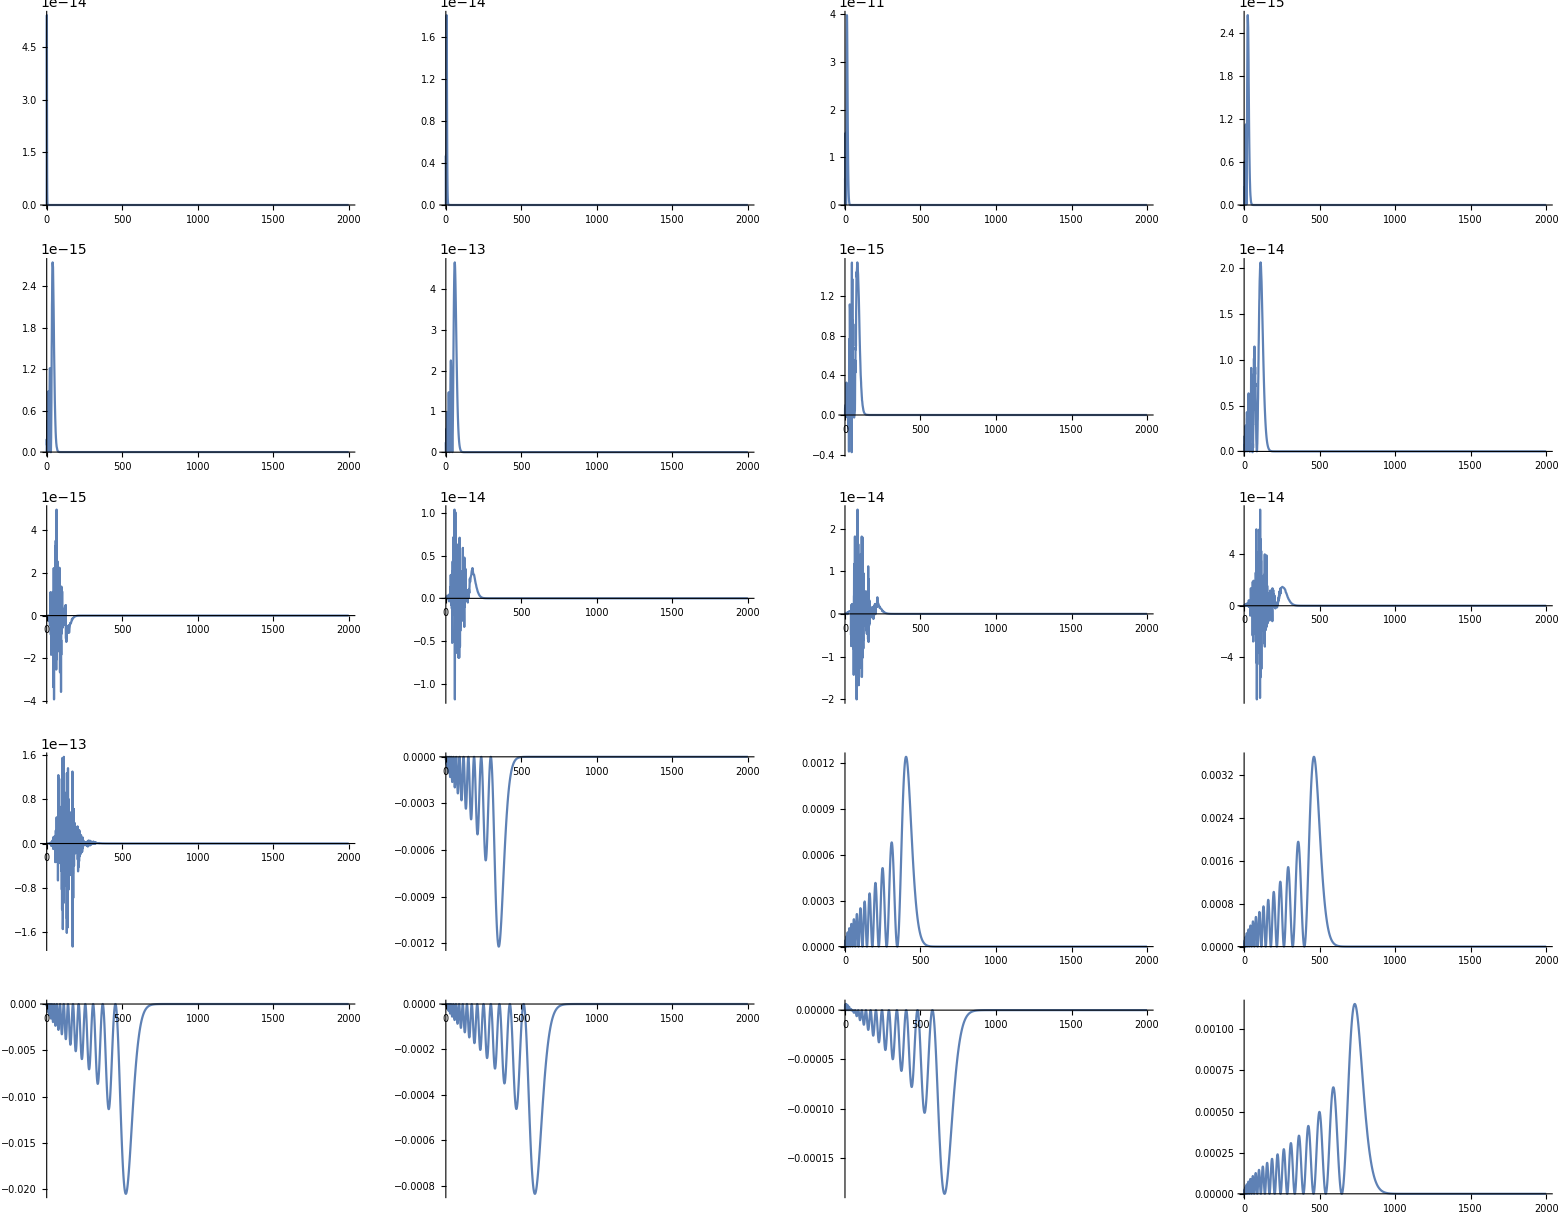

```mathematica
GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)^2-(am[[n]]f[r])^2/.eigenfunV[[n]],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

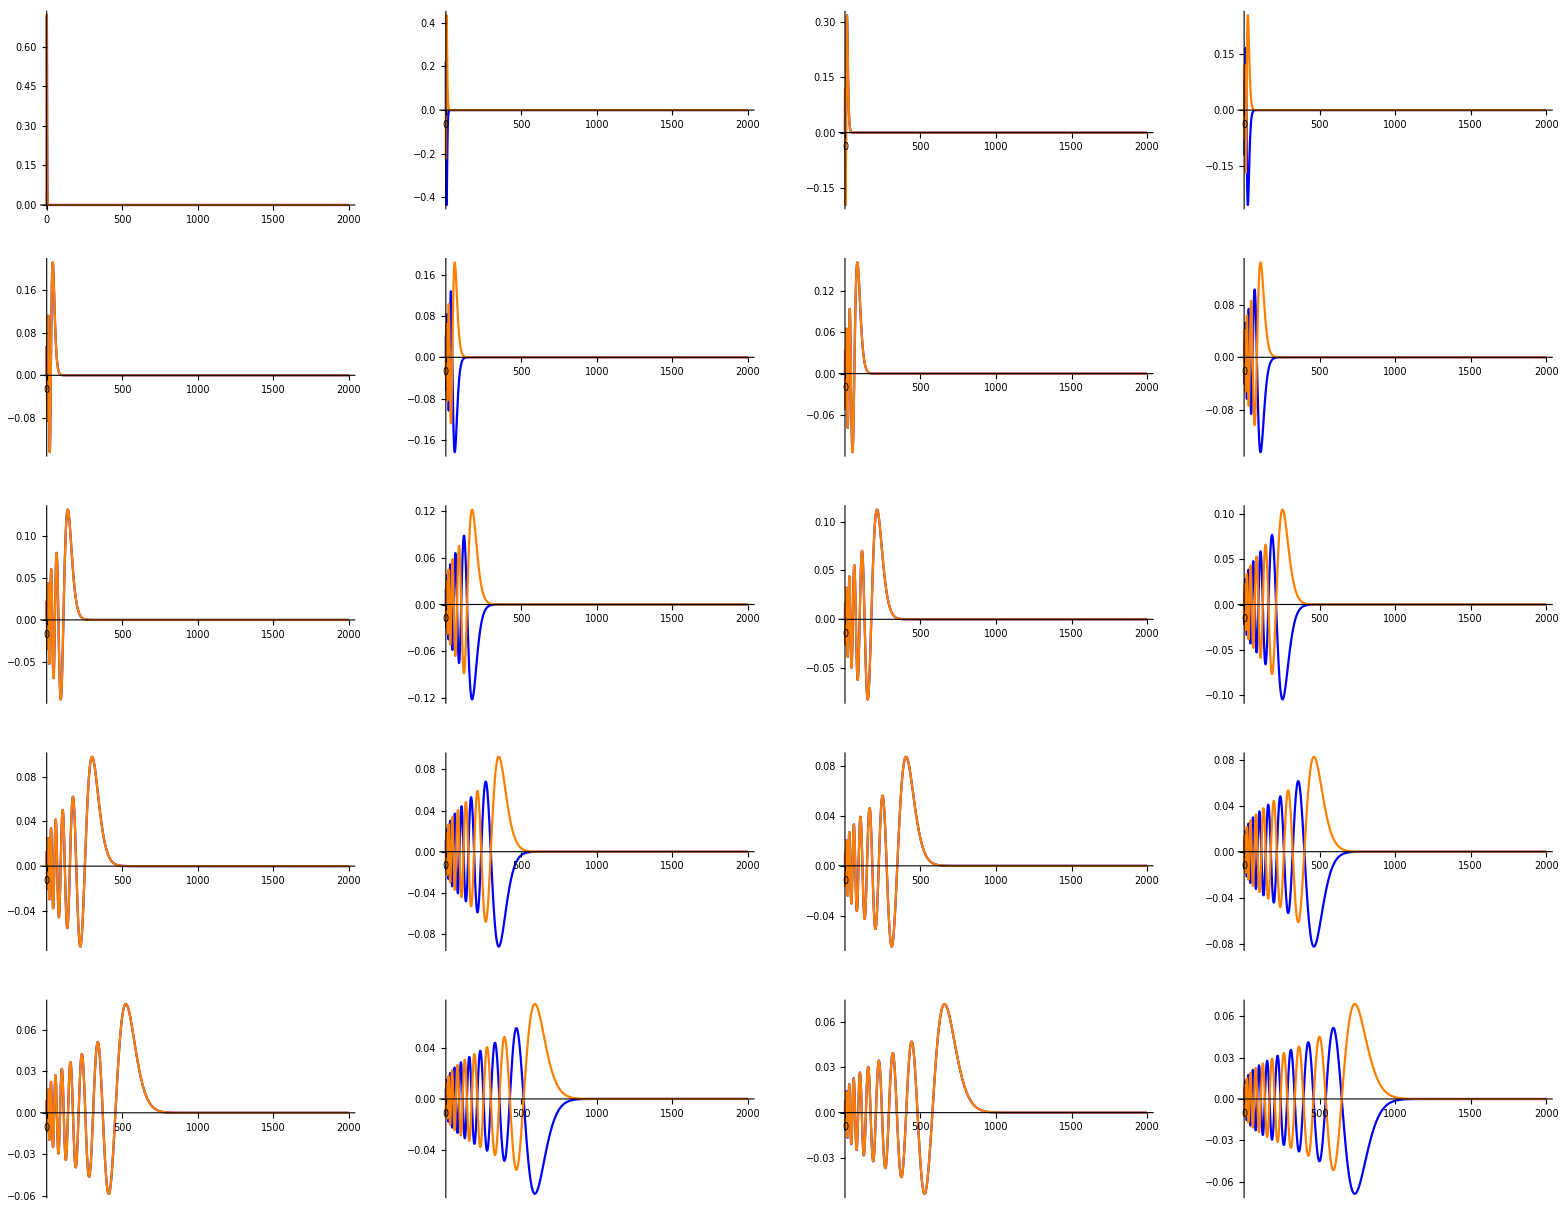
{1290.38,-Graphics-}

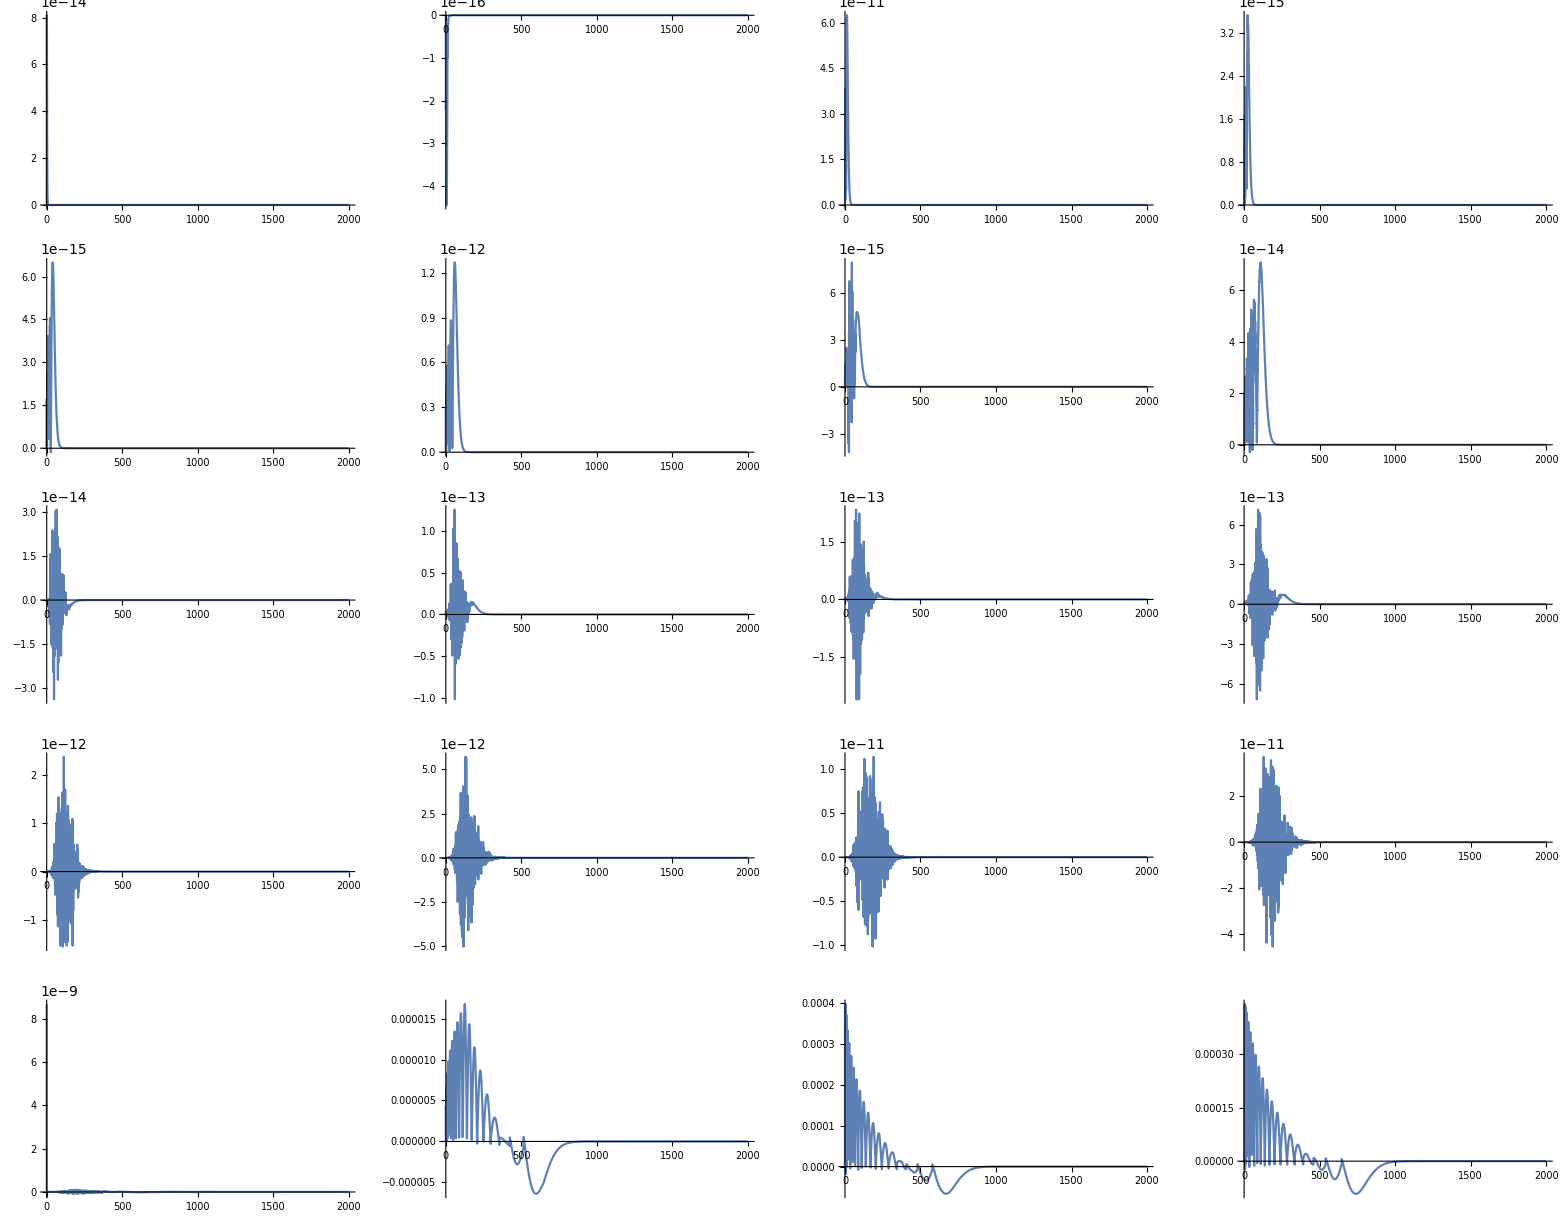
{1219.42,-Graphics-}

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),(am[[n]]f[r])/.eigenfunV[[n]]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[Abs@(RS[n,r]r)-Abs@(am[[n]]f[r])/.eigenfunV[[n]],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

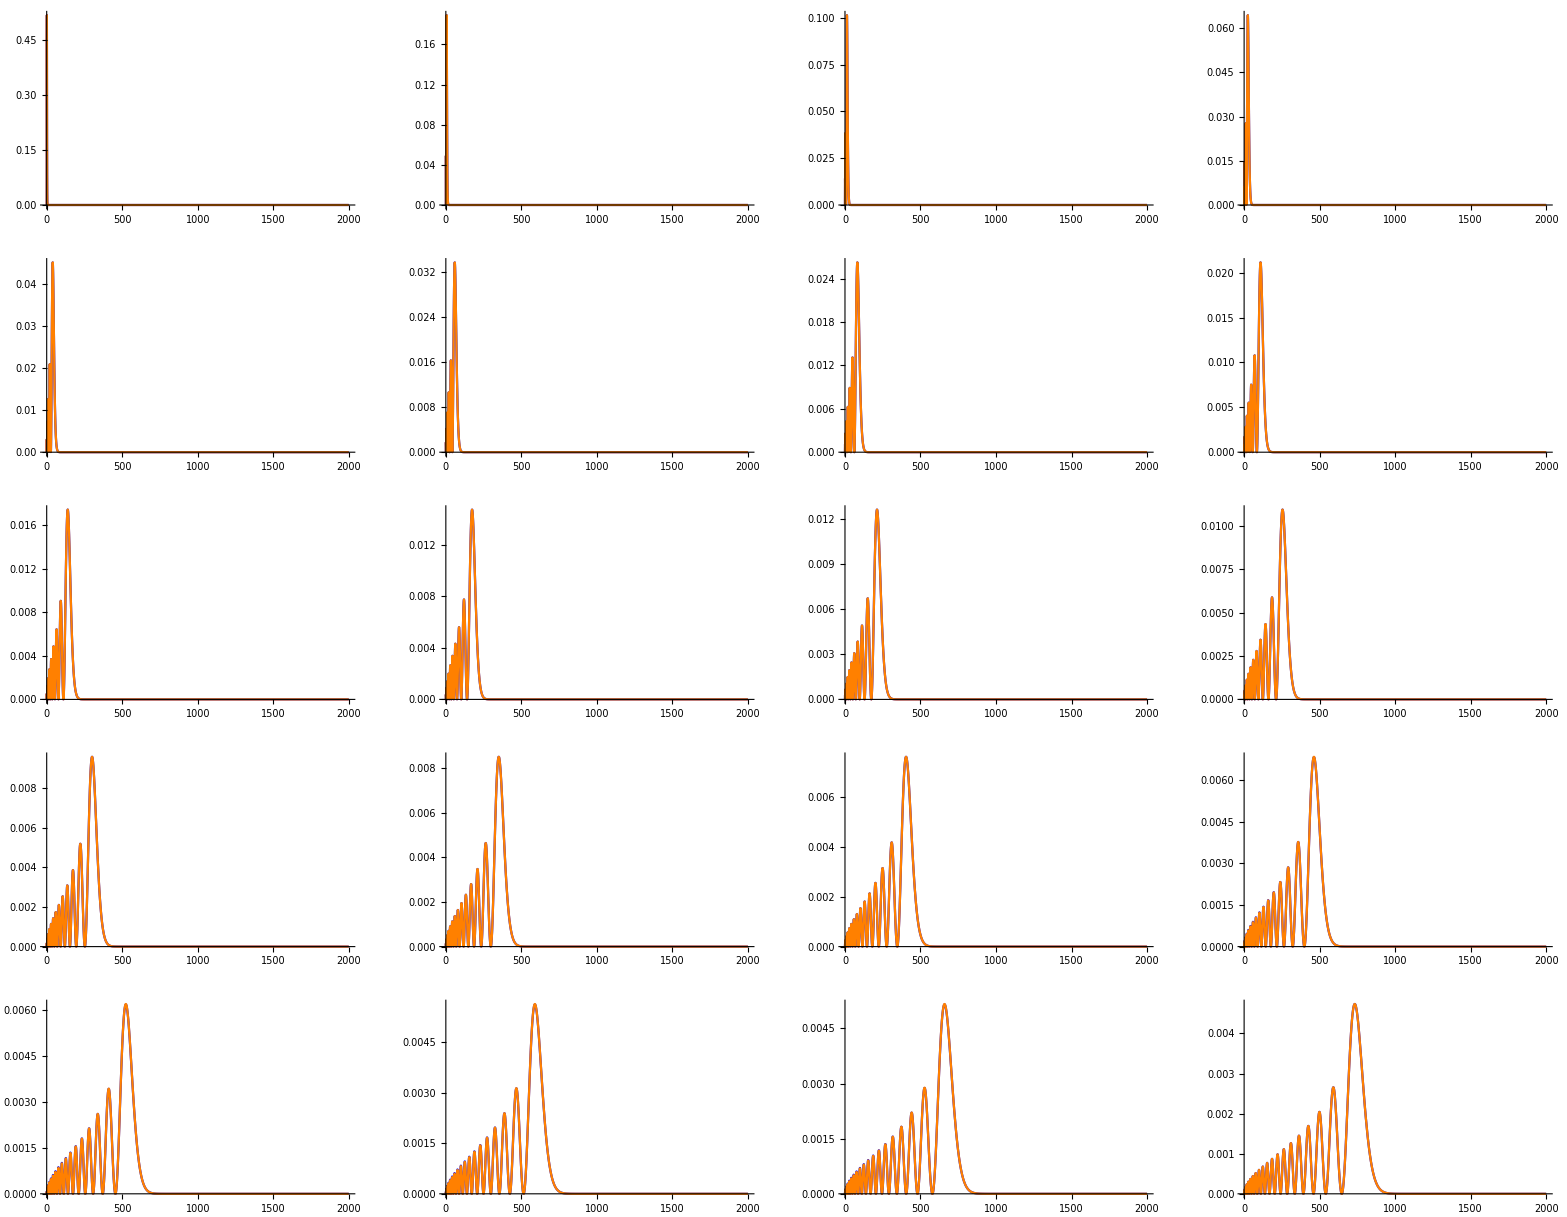

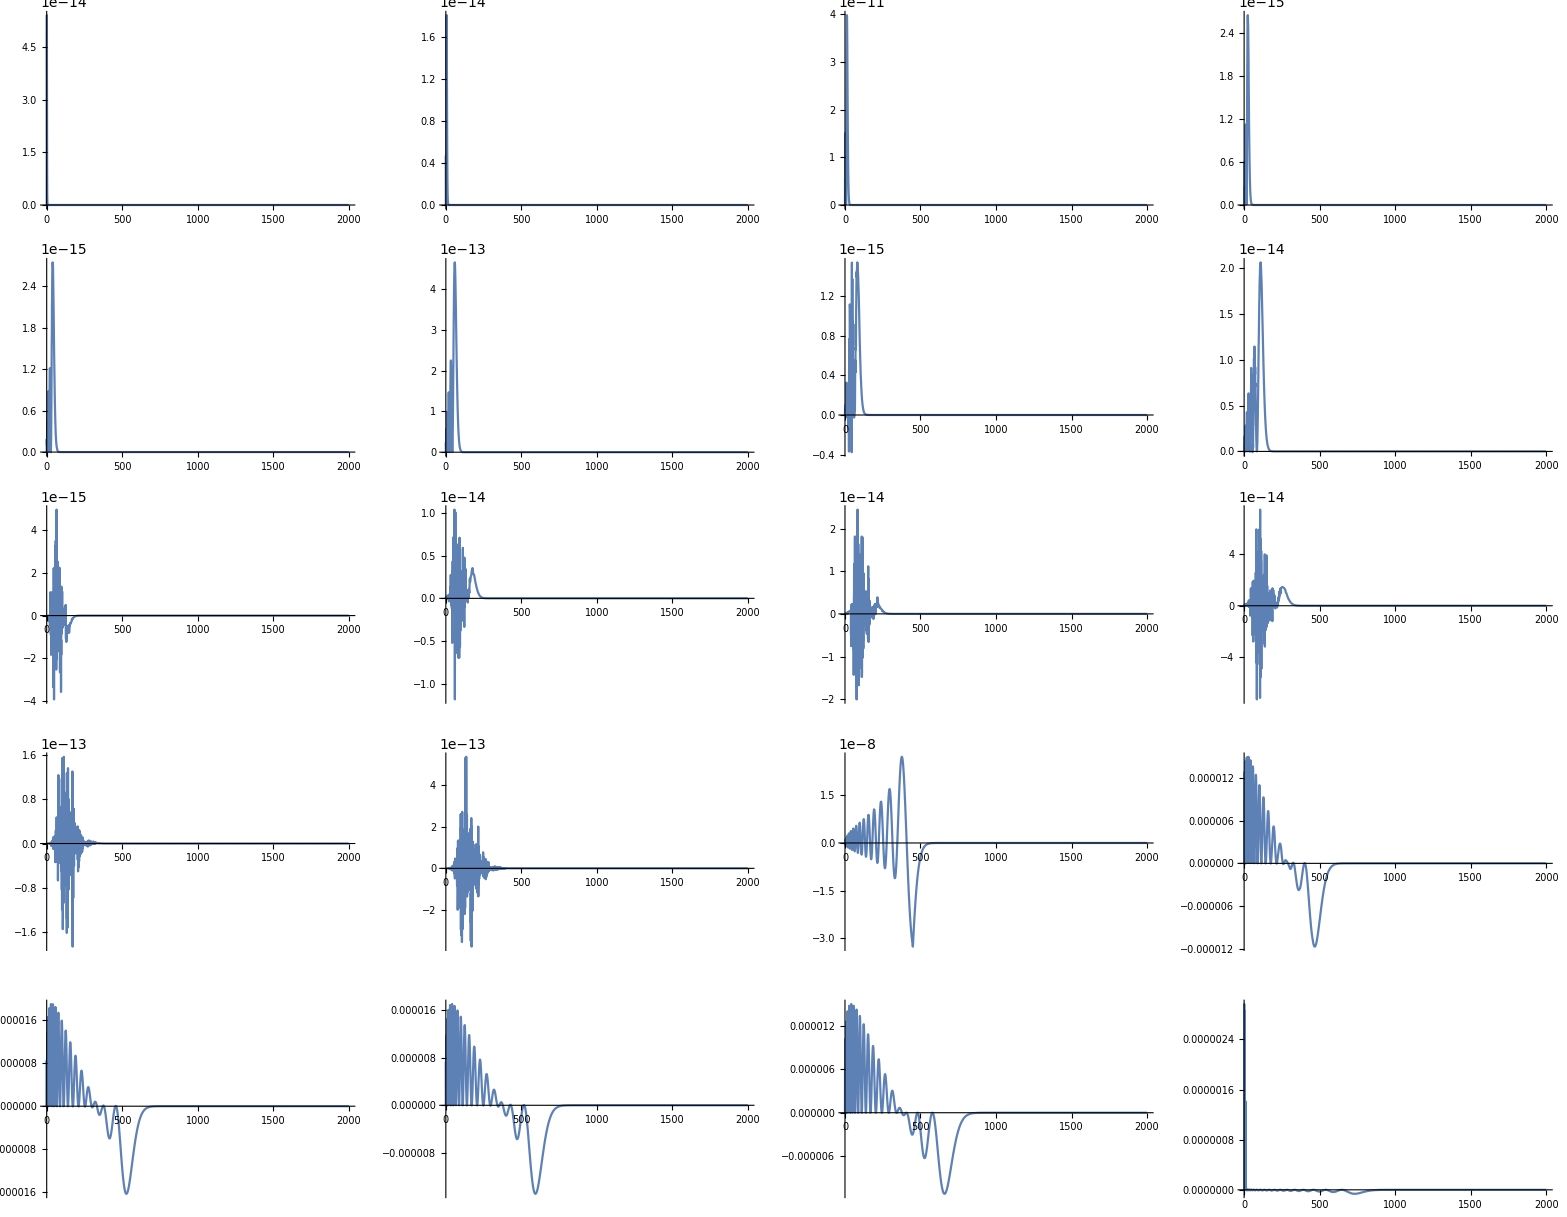

```mathematica
(*{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,*)
(*Square*)
```

```mathematica
Table[NIntegrate[RS[n,r]^2 r^2,{r,1.*10^-50,2000}],{n,20}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

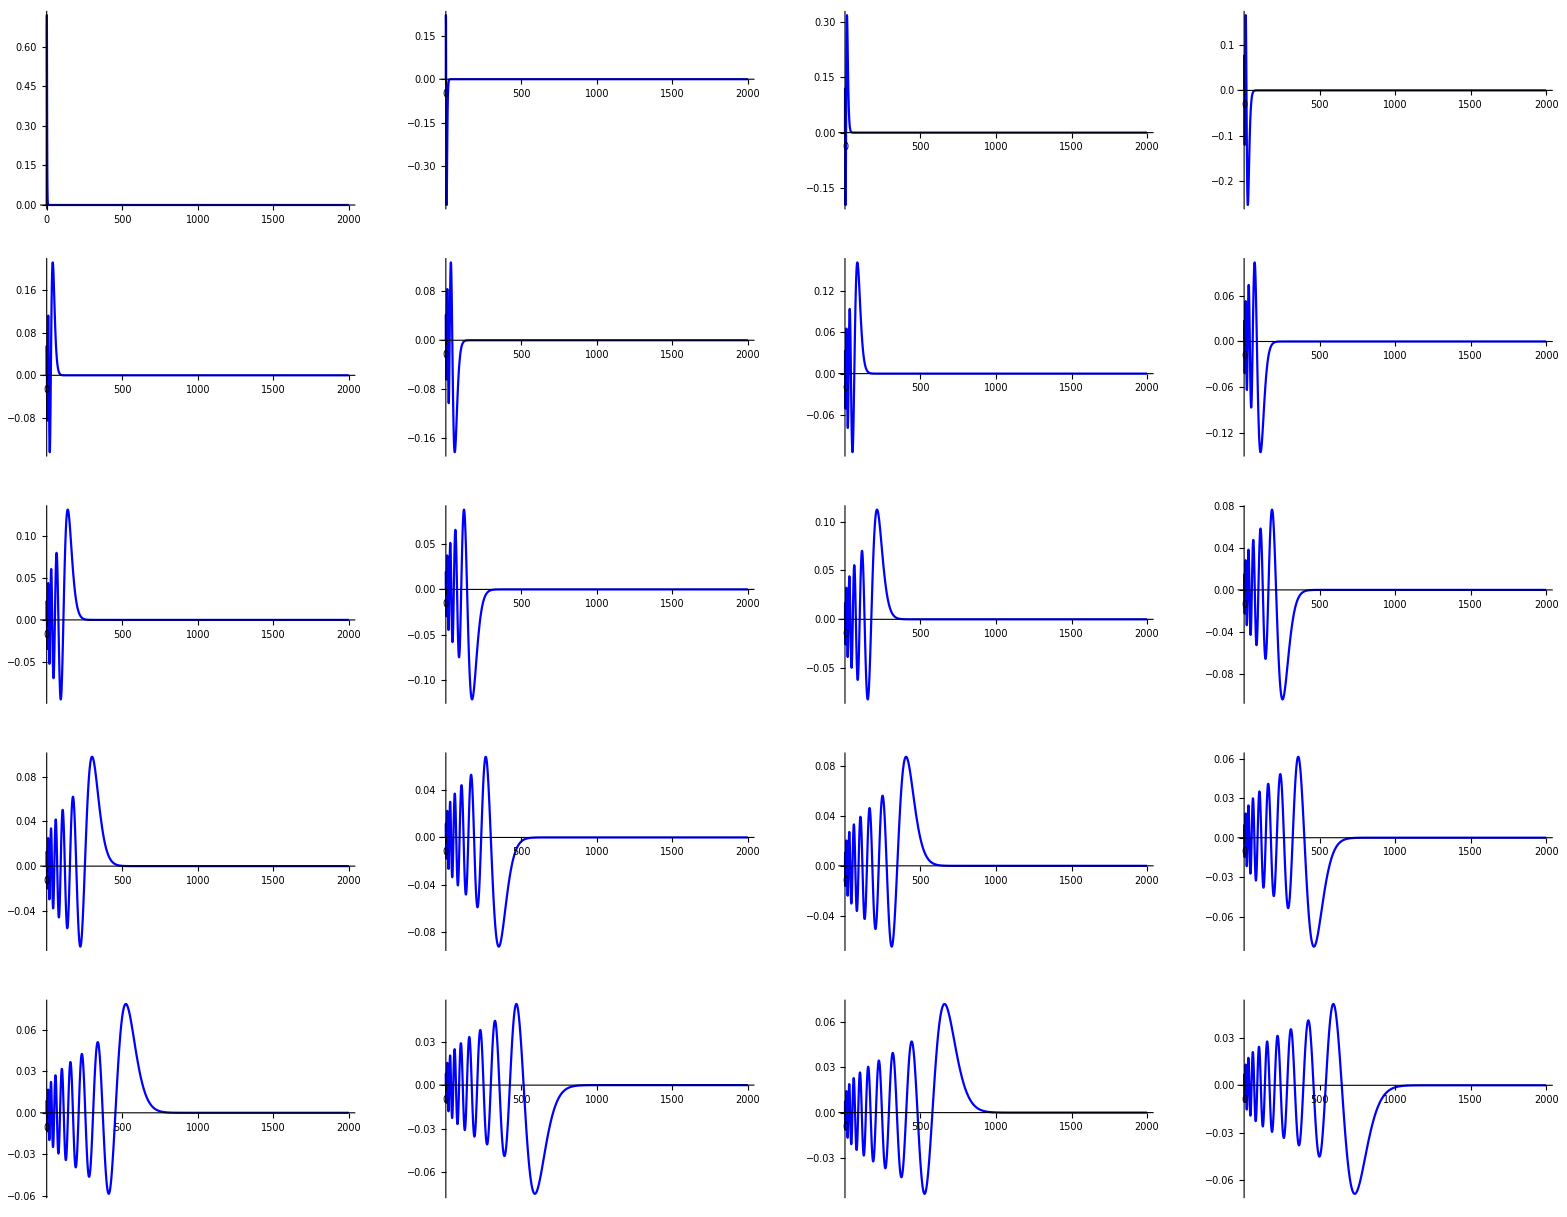

```mathematica
GraphicsGrid@Partition[Table[Plot[{RS[n,r]r},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue}],{n,20}],4]
```